# Calculation of Statistical-Mechanical Quantities of Lotka-Volterra Hamiltonian

## (#1): Requisite Data:

## (#1.1): “Standard LV Hamiltonian”

### (#1.1.1): Defining the Hamiltonian:

```mathematica
LVHamiltonian[q_,p_]:=δ Exp[p]-γ p + β Exp[q]-α q;
```

### (#1.1.2): Can we easily exponentiate it without Mathematica freaking out?

```mathematica
Exp[LVHamiltonian[q,p]]
```

ⅇ^(-q α+ⅇ^q β-p γ+ⅇ^p δ)

## (#2): Microcanonical Ensemble Analysis (“Standard Hamiltonian”):

## (#2.1): Obtaining the Area Enclosed by Phase Space Orbits:

### (#2.1.1): Making a plot for visualizing the orbits:

Using the following article for the values of the parameter: https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example

#### (#2.1.1.1): The LV Hamiltonian:

For initial conditions of p = 0.9 and q = 0.9, the constant of the motion under the designation of the four model parameters below is:

```mathematica
LVHamiltonian[0.9,0.9]/.α->2/3/.β->4/3/.γ->1/.δ->1
```

4.23907

#### (#2.1.1.2): The Plot: ([NOTE]: New phase space variables can be negative and positive!)

The space is foliated, but it looks like a strange shape (i.e. not ellipsoidal, obviously). Topologically equivalent to torus, probably.

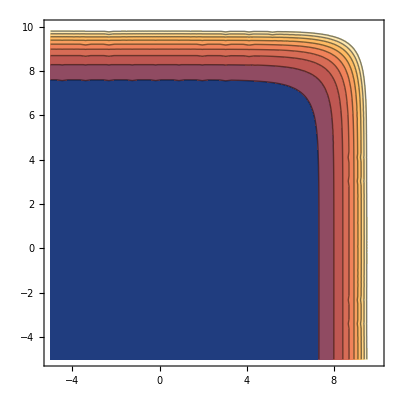

```mathematica
ContourPlot[ⅇ^p+(4 ⅇ^q)/3-p-(2 q)/3,{q,-5,10},{p,-5,10}]
```

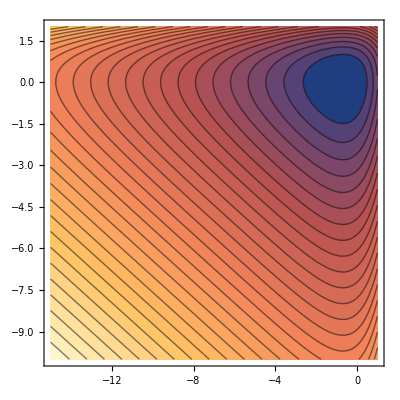

```mathematica
(* α = 2/3, β = 4/3, γ = δ = 1*)
(* These parameters are the ones used in the paper, Figure 1 *)
ContourPlot[1 ⅇ^p-1 p+4/3 Exp[q]-2/3 q,{q,-15,1},{p,-10,2},Contours->30]
```

### (#2.1.2): Trying to Solve for the Bounding Functions:

#### (#2.1.2.1): Seeing how many Solutions are found for the Implicit Equation:

```mathematica
FullSimplify[
Solve[ConstE==LVHamiltonian[q,p],p],
Assumptions-> 
-∞<q<∞&&-∞<p<∞&&
ConstE∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&δ∈PositiveReals&&γ∈PositiveReals]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→InverseFunction[LVHamiltonian,2,2][q,ConstE]}}

Only one solution is found... That is likely because, although we specified that α, β, γ, and δ are positive, we did not specify their relative differences.

```mathematica
LVHamiltonian[q,p]/.p->-(ConstE+q α-ⅇ^q β+γ ProductLog[0,-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ//Simplify
```

ConstE

```mathematica
LVHamiltonian[q,p]/.p->-(ConstE+q α-ⅇ^q β+γ ProductLog[1,-(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ])/γ//Simplify
```

ConstE

Wow! It actually works. Nice!

#### (#2.1.2.2): Manually Entering the Solutions We Got:

```mathematica
pPlus=(-ConstE+β Exp[q]-α q)/γ-ProductLog[0,δ/γ Exp[(-ConstE+β Exp[q]-α q)/γ]];
pMinus=(-ConstE+β Exp[q]-α q)/γ-ProductLog[1,δ/γ Exp[(-ConstE+β Exp[q]-α q)/γ]];
```

#### (#2.1.2.3): Since the first integral is just over 1, the integrand for the next integral is just p^+-p^-. So, what is that?

```mathematica
FullSimplify[
pPlus-pMinus,
Assumptions->ConstE∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&γ∈PositiveReals&&δ∈PositiveReals
]
```

-ProductLog[(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]

#### (#2.1.2.4): Test Run Using a Dummy Integrand, ∫dx (-W_0(x)+W_1(x)):

Below, x stands for the insane thing in the ProductLog[].

```mathematica
FullSimplify[
Integrate[
-ProductLog[0,x]+ProductLog[1,x],
{x, a, b}],
Assumptions->a>0&&b>0&&b>a]
```

ⅇ^ProductLog[a]-ⅇ^ProductLog[b]-ⅇ^ProductLog[1,a]+ⅇ^ProductLog[1,b]+a ProductLog[a]-b ProductLog[b]-a ProductLog[1,a]+b ProductLog[1,b]

#### (#2.1.2.5): Trying the whole thing:

```mathematica
Integrate[
-ProductLog[0,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ],
{q, -5,5},
Assumptions->
ConstE∈Reals&&
α∈Reals&&β∈Reals&&δ∈Reals&&γ∈Reals
]
```

Integrate[-ProductLog[(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ]+ProductLog[1,(ⅇ^(-(ConstE+q α-ⅇ^q β)/γ) δ)/γ],{q,-5,5},Assumptions→ConstE∈ℝ&&α∈ℝ&&β∈ℝ&&δ∈ℝ&&γ∈ℝ]

#### (#2.1.2.6): Can we get something closed-form of (∫_a)^b dxW^(e^(-h x))?

It seems like we can:

```mathematica
Integrate[
ProductLog[0,Exp[-h x]],{x, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

((ProductLog[ⅇ^(-a h)]-ProductLog[ⅇ^(-b h)]) (2+ProductLog[ⅇ^(-a h)]+ProductLog[ⅇ^(-b h)]))/(2 h)

#### (#2.1.2.7): How about the indefinite form of this: ∫dxW^(e^(-h x))?

I also managed to derive this. Yay!

```mathematica
Integrate[
ProductLog[0,Exp[a x]],x,
Assumptions->a∈Reals]
```

ProductLog[ⅇ^(a x)]/a+(ProductLog[ⅇ^(a x)]^2)/(2 a)

#### (#2.1.2.8): Can we get something closed-form of ∫dxW^(e^(e^x))?

Here, we cannot get it.

```mathematica
Integrate[
ProductLog[Exp[Exp[x]+x]],{x, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[ProductLog[ⅇ^(ⅇ^x+x)],{x,a,b},Assumptions→a>0&&b>0&&b>a]

#### (#2.1.2.9): After some u-substitution, I think we can get ∫dxW^(e^(e^x))into something like this:

And this has at least some kind of crazy solution:

```mathematica
(*
Integrate[
Log[ProductLog[x]]/ProductLog[x],{x, a, b},
Assumptions->a>0&&b>0&&b>a]
*)
```

#### (#2.1.2.10): After a u-substitution on ∫dx W(a^(e^(e^bx+cx))), I found this integral:

It still can’t get it, but it must be possible...

```mathematica
Integrate[
Exp[u]ProductLog[0,u],{u, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[ⅇ^u ProductLog[u],{u,a,b},Assumptions→a>0&&b>0&&b>a]

```mathematica
Integrate[
v^2 Exp[Exp[v]+v],{v, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[ⅇ^(ⅇ^v+v) v^2,{v,a,b},Assumptions→a>0&&b>0&&b>a]

```mathematica
Integrate[
v^v Log[V],{v, a, b},
Assumptions->
a>0&&
b>0&&
b>a]
```

Integrate[v^v Log[V],{v,a,b},Assumptions→a>0&&b>0&&b>a]

```mathematica
Integrate[
Log[u]ProductLog[A Exp[u]],{u, a, b},
Assumptions->
A>0&&a>0&&b>0&&b>a]
```

Integrate[Log[u] ProductLog[A ⅇ^u],{u,a,b},Assumptions→A>0&&a>0&&b>0&&b>a]

### (#2.1.3): Let’s briefly take a simpler approach:

#### (#2.1.3.1): Solving for the Boundaries using Kerner’s Hamiltonian:

```mathematica
FullSimplify[
Solve[ConstE==γ(Exp[p]-p) + α(Exp[q]-q),p],
Assumptions-> 
-∞<q<∞&&-∞<p<∞&&
ConstE∈PositiveReals&&α∈PositiveReals&&γ∈PositiveReals]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→-(ConstE+(-ⅇ^q+q) α+γ ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)])/γ}}

#### (#2.1.3.2): Manually entering the solutions:

```mathematica
pPlusDimensionless=-(ConstE+(-ⅇ^q+q) α+γ ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)])/γ;
pMinusDimensionless=(ConstE+(-ⅇ^q+q) α+γ ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)])/γ;
```

#### (#2.1.3.3): Constructing the integrand:

```mathematica
FullSimplify[
pPlusDimensionless-pMinusDimensionless,
Assumptions->ConstE∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&γ∈PositiveReals&&δ∈PositiveReals
]
```

-(2 (ConstE+(-ⅇ^q+q) α+γ ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]))/γ

#### (#2.1.3.4): Separating out the two terms to see if it will help with integration:

```mathematica
-2((ConstE+(-ⅇ^q+q) α)/γ+γ ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)]/γ)
```

-2 ((ConstE+(-ⅇ^q+q) α)/γ+ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)])

#### (#2.1.3.5): Integrating the first piece:

```mathematica
Integrate[
-2 ((ConstE+(-ⅇ^q+q) α)/γ),
{q, -a,a},
Assumptions->ConstE∈PositiveReals&&α∈PositiveReals&&γ∈PositiveReals&&a∈PositiveReals
]
```

(-4 a ConstE+4 α Sinh[a])/γ

Wow. I didn’t expect that.

#### (#2.1.3.6): Taking the limit:

```mathematica
Limit[(-4 a ConstE+4 α Sinh[a])/γ,a->∞]
```

(α ∞)/γ

Actually, this limit is not correct here. The integral over q will have finite bounds because the area enclosed is finite. So, maybe we shouldn’t freak out just yet.

#### (#2.1.3.7): But the W(x) thing is still too difficult for the notebook to do!

```mathematica
Integrate[
-2(ProductLog[0,-Exp[-(ConstE-ⅇ^q α+q α)/γ]]),
{q, 5,6},
Assumptions->ConstE∈Reals&&α∈Reals&&γ∈Reals
]
```

Integrate[-2 ProductLog[-ⅇ^(-(ConstE-ⅇ^q α+q α)/γ)],{q,5,6},Assumptions→ConstE∈ℝ&&α∈ℝ&&γ∈ℝ]

## (#2.2): Suppose it’s an “ecological ideal gas,” where no q is featured in H:

We pretend that, just for computation’s sake, that there is no q in the Hamiltonian, or rather that q only ranges from 0 to some fixed “box” size of length L.

### (#2.2.1): Solving for the maximum value p can take with a fixed E:

```mathematica
Solve[ConstE==δ Exp[p]-γ p ,p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→(-ConstE-γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/γ}}

#### (#2.2.1.1): Verifying the upper bound is correct:

```mathematica
δ Exp[p]-γ p /.p->(-ConstE-γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/γ//Simplify
```

ConstE

#### (#2.2.1.2): Verifying the lower bound is correct:

```mathematica
δ Exp[p]-γ p /.p->(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ//Simplify
```

ConstE

#### (#2.2.1.3): What happens when E is quite small? Does it go back to something like √(2mE)?

```mathematica
Series[(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ,{ConstE,0,1}]//FullSimplify
```

-ProductLog[1,-δ/γ]-ConstE/(γ+γ ProductLog[1,-δ/γ])+O[ConstE]^2

#### (#2.2.1.4): Want to see the contours:

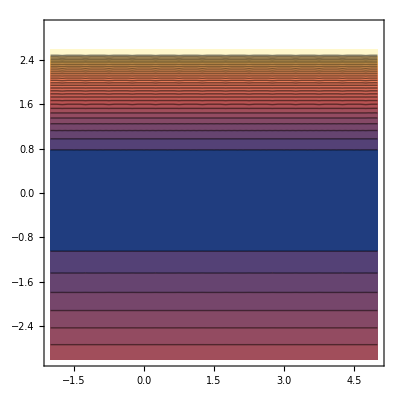

```mathematica
ContourPlot[1 ⅇ^p-1 p,{q,-2,5},{p,-3,3},Contours->30]
```

#### (#2.2.1.5): How about the contours with very small q?

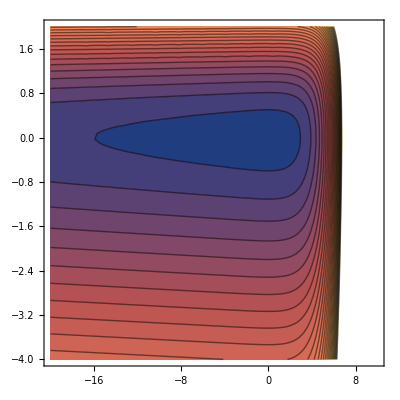

```mathematica
ContourPlot[1 ⅇ^p-1 p+0.01Exp[q]-0.01q,{q,-20,10},{p,-4,2},Contours->30]
```

#### (#2.2.1.6): Same thing except for small p:

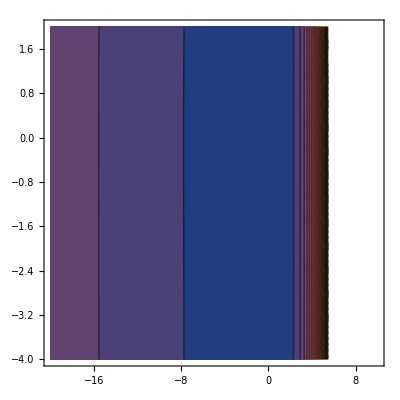

```mathematica
ContourPlot[0.01 ⅇ^p-0.01p+1Exp[q]-1 q,{q,-20,10},{p,-4,2},Contours->30]
```

### (#2.2.2): Let’s now construct the bounding box, bounded specifically by a “volume” of length L:

#### (#2.2.2.1): Computation of Γ(E):

```mathematica
FullSimplify[
2((-ConstE-γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/γ*(-ConstE-γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/γ)/(Δq Δp),
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals&&δ∈Reals]
```

(2 (ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ]) (ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))/(γ^2 Δp Δq)

#### (#2.2.2.2): Computation of g(E)=(dΓ(E))/dE:

```mathematica
FullSimplify[
D[(2 (ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ]) (ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))/γ^2,{ConstE,1}],
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals&&δ∈Reals
]
```

(2 (ConstE/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])))/γ^2

Let me quickly rewrite this thing:

```mathematica
2/γ^2((ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[0,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))-FullSimplify[
D[(2 (ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ]) (ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ]))/γ^2,{ConstE,1}],
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals&&δ∈Reals
]
```

-(2 (ConstE/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])))/γ^2+(2 ((ConstE+γ ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])+(ConstE+γ ProductLog[1,-(ⅇ^(-ConstE/γ) δ)/γ])/(1+ProductLog[-(ⅇ^(-ConstE/γ) δ)/γ])))/γ^2

## (#2.3): Now suppose that the momentum is quadratic but the potential is the normal U(q):

### (#2.3.1): Making a plot for visualizing the orbits:

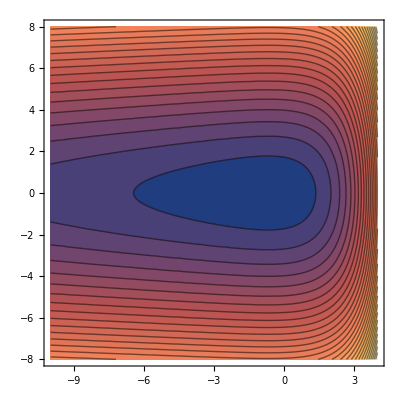

```mathematica
(* α = 2/3, β = 4/3, γ = δ = 1*)
(* These parameters are the ones used in the paper, Figure 1 *)
ContourPlot[δ p^2+β Exp[q]-α q/.α->2/3/.β->4/3/.γ->1/.δ->1,{q,-10,4},{p,-8,8},Contours->30]
```

### (#2.3.2): Trying to Solve for the Bounding Functions:

#### (#2.3.2.1): Seeing how many Solutions are found for the Implicit Equation:

```mathematica
FullSimplify[
Solve[ConstE==δ p^2+β Exp[q]-α q,p],
Assumptions-> 
-∞<q<∞&&-∞<p<∞&&
ConstE∈Reals&&α∈Reals&&β∈Reals&&δ∈Reals&&γ∈Reals]
```

{{p→-(√(ConstE+q α-ⅇ^q β))/(√δ)},{p→(√(ConstE+q α-ⅇ^q β))/(√δ)}}

Let’s now check to see if we get the right results:

```mathematica
δ p^2+β Exp[q]-α q/.p->-(√(ConstE+q α-ⅇ^q β))/(√δ)//Simplify
```

ConstE

```mathematica
δ p^2+β Exp[q]-α q/.p->+(√(ConstE+q α-ⅇ^q β))/(√δ)//Simplify
```

ConstE

The two solutions differ by the ± sign, and the momentum is squared, so these will of course give the same thing, namely ConstE.

#### (#2.3.2.2): Manually Entering the Solutions We Got:

```mathematica
microPPlus=(√(ConstE+q α-ⅇ^q β))/(√δ);
microPMinus=-(√(ConstE+q α-ⅇ^q β))/(√δ);
```

#### (#2.3.2.3): Since the first integral is just over 1, the integrand for the next integral is just p^+-p^-. So, what is that?

```mathematica
FullSimplify[
microPPlus-microPMinus,
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&γ∈Reals&&δ∈Reals
]
```

(2 √(ConstE+q α-ⅇ^q β))/(√δ)

#### (#2.3.2.4): Let’s do a test run with the integral over q, just to see if it is possible:

```mathematica
FullSimplify[
Integrate[(2 √(ConstE+q α-ⅇ^q β))/(√δ),{q, a, b}],
Assumptions->ConstE∈Reals&&α∈Reals&&β∈Reals&&δ∈Reals&&a∈PositiveReals&&b∈PositiveReals&&b>a
]
```

∫_a^b (2 √(ConstE+q α-ⅇ^q β))/(√δ)ⅆq

Rewriting...

```mathematica
√(ConstE+q α-ⅇ^q β)-√(-β(Exp[q]-α/β q-ConstE/β))//FullSimplify
```

0

```mathematica
FullSimplify[
Integrate[2/(√δ)√(-β(Exp[q]-α/β q-ConstE/β)),{q, a, b}],
e..
]
```

∫_a^b (2 √(ConstE+q α-ⅇ^q β))/(√δ)ⅆq

```mathematica
Series[Sqrt[1+x],{x,0,5}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256+O[x]^6

```mathematica
FullSimplify[Series[Sqrt[Exp[x]-x-1],{x,0,5}],Assumptions->x∈Reals]
```

Abs[x] (1/(√2)+x/(6 √2)+x^2/(36 √2)+x^3/(270 √2)+x^4/(2592 √2)+O[x]^6)

## (#3): Canonical Ensemble Analysis:

## (#3.1): Partition Function:

### (#3.1.1): Defining the entire Partition Function:

```mathematica
LVZ[σ_]:=Exp[-σ LVHamiltonian[q,p]]
```

### (#3.1.2): Defining the Z_p Part:

```mathematica
LVZp[σ_]:=Exp[-σ(δ Exp[p]-γ p)]
```

### (#3.1.3): Defining the Z_q Part:

```mathematica
LVZq[σ_]:=Exp[-σ(β Exp[q]-α q)]
```

### (#3.1.4): Integrating the Z_p Part:

```mathematica
LVZpIntegral=Integrate[LVZp[σ],{p,-∞,∞},Assumptions->σ∈PositiveReals&&δ∈PositiveReals&&γ∈PositiveReals]
```

(δ σ)^(-γ σ) Gamma[γ σ]

### (#3.1.5): Integrating the Z_q Part:

```mathematica
LVZqIntegral=Integrate[LVZq[σ],{q,-∞,∞},Assumptions->σ∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals]
```

(β σ)^(-α σ) Gamma[α σ]

### (#3.1.6): Cross-checking: Z_p Z_q should equal Z:

```mathematica
LVZIntegral=Integrate[LVZ[σ],{q,-∞,∞},{p,-∞,∞},Assumptions->σ∈PositiveReals&&α∈PositiveReals&&β ∈PositiveReals&&δ∈PositiveReals&&γ∈PositiveReals]
```

(β σ)^(-α σ) (δ σ)^(-γ σ) Gamma[α σ] Gamma[γ σ]

We need to confirm that the result is the same as doing the single integral all at once.

```mathematica
LVZpIntegral LVZqIntegral - LVZIntegral
```

0

### (#3.1.7): Plotting Z(σ) with some test parameters:

According to the [following link on the Wiki page about the LV equations](https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations#Phase-space_plot_of_a_further_example), there are closed cycles for α = 2/3, β = 4/3, γ = 1, and δ = 1. So, let’s use those values while checking these plots.

#### (#3.1.7.1): Plotting Z(σ) with test parameters:

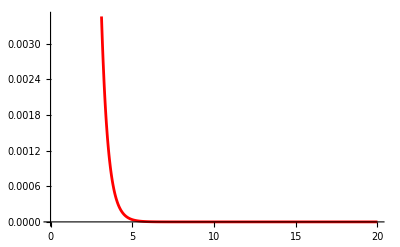

```mathematica
Plot[
LVZIntegral/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0,20},
PlotStyle->Red
]
```

#### (#3.1.7.2): Plotting Z(T) — remember that σ = 1/(k_B T)—with test parameters:

General::munfl: 1/99.7982^166.33 is too small to represent as a normalized machine number; precision may be lost.

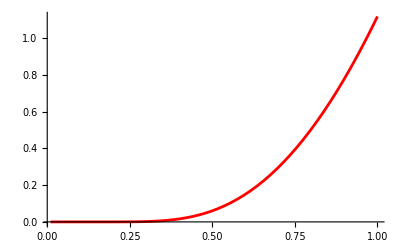

```mathematica
Plot[
LVZIntegral/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.01,1.00},
PlotStyle->Red
]
```

## (#3.2): Average Energy, ⟨E⟩=-∂/(∂ β)log(Z):

### (#3.2.1): Quantitative calculation using the standard formula:

```mathematica
LVEnergyAverage=-D[Log[LVZIntegral],σ]//FullSimplify
```

α+γ+α Log[β σ]+γ Log[δ σ]-α PolyGamma[0,α σ]-γ PolyGamma[0,γ σ]

Just need to check if I can simplify this with another form:

```mathematica
(α(1+Log[β σ]-PolyGamma[0,α σ])+γ(1+Log[δ σ]-PolyGamma[0,γ σ]) )-LVEnergyAverage//FullSimplify
```

0

### (#3.2.2): Plotting ⟨E⟩(σ) with some test parameters:

#### (#3.2.2.1): Plotting ⟨E⟩(σ.) with test parameters:

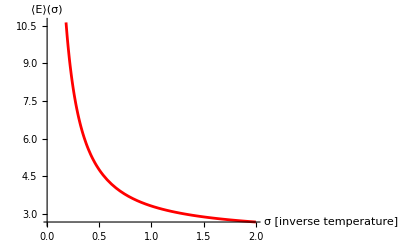

```mathematica
Plot[
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.01,2},
PlotStyle->Red,
AxesLabel->{"σ [inverse temperature]","⟨E⟩(σ)"}
]
```

#### (#3.2.2.2): Plotting ⟨E⟩(T) — remember that σ = 1/(k_B T)—with test parameters:

[NOTE]: It appears there is no minimum average energy.

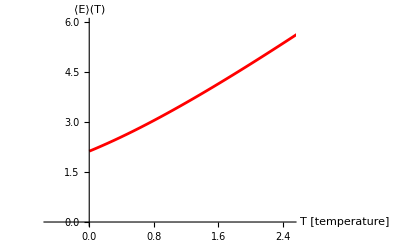

```mathematica
Plot[
LVEnergyAverage/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,-1,3},
PlotStyle->Red,
AxesLabel->{"T [temperature]","⟨E⟩(T)"},
PlotRange->{{-0.5,2.5},{0,6}}
]
```

At zero temperature, the average energy is not zero. So, can we find the value of the thing at T = 0?
First, let’s get the analytical expression in terms of Temperature:

```mathematica
LVEnergyAverage/.σ->1/T
```

α+γ+α Log[β/T]+γ Log[δ/T]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T]

Now, obviously evaluating this for T = 0 will lead to divergences. So, let’s determine its value numerically with a very small value for T.

```mathematica
LVEnergyAverage/.σ->1/T/.T->0.0000000000000000001
```

α+γ+α Log[1.×10^19 β]+γ Log[1.×10^19 δ]-α PolyGamma[0,1.×10^19 α]-γ PolyGamma[0,1.×10^19 γ]

That looks like it corresponds with what the plot is showing. Alright. Good check.

Next, let’s take a limit.

```mathematica
Limit[LVEnergyAverage/.σ->1/T,T->0]
```

lim_(T→0) (α+γ+α Log[β/T]+γ Log[δ/T]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T])

Riiiight. That’s expected. [NOTE]: And it turns out that it actually has to do with the direction of the limit! That is, we need to take the limit from the right!
Let’s just try to copy/paste the analytical thing we got earlier:

```mathematica
Limit[
α+γ+α Log[β/T]+γ Log[δ/T]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T],
T->0,
(* This strange word means "take limit from the right" *)
 Direction->-1]
```

ConditionalExpression[α+γ-α Log[α]+α Log[β]-γ Log[γ]+γ Log[δ], α>0&&β>0&&γ>0&&δ>0]

This should match with the earlier result, so their difference should be 0:

```mathematica
Limit[α+γ+α Log[β/T]+γ Log[δ/T]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T],T->0,Direction->-1]-Limit[LVEnergyAverage/.σ->1/T,T->0, Direction->-1]
```

ConditionalExpression[0, α>0&&β>0&&γ>0&&δ>0]

Can we see if this is the number that appears on the plot earlier:

```mathematica
N[α+γ-α Log[α]+α Log[β]-γ Log[γ]+γ Log[δ]/.α->2/3/.β->4/3/.γ->1/.δ->1]
```

2.12876

Yes, that actually looks about right...

Let’s find the low-temperature behavior by expanding E(T) about T = 0.

```mathematica
Series[LVEnergyAverage/.σ->1/T,{T,0,1}]
```

ⅈ π α Floor[Abs[Arg[α/T]]/π]+π α Cot[(π α)/T+O[T]^2] Floor[Abs[Arg[α/T]]/π]+ⅈ π γ Floor[Abs[Arg[γ/T]]/π]+π γ Cot[(π γ)/T+O[T]^2] Floor[Abs[Arg[γ/T]]/π]+((α+γ-α Log[α/T]+α Log[β/T]-γ Log[γ/T]+γ Log[δ/T])+T+O[T]^2)

Oh, nuts. There is some parameter thing going on here... Seems like the heat-capacity may become imaginary if γ in relation to T is not nice...

```mathematica
Limit[α+γ-α Log[α/T]+α Log[β/T]-γ Log[γ/T]+γ Log[δ/T]+T,T->0,Direction->-1]
```

α+γ-α Log[α]+α Log[β]-γ Log[γ]+γ Log[δ]

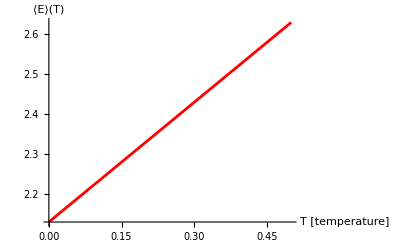

```mathematica
Plot[
(α+γ-α Log[α/T]+α Log[β/T]-γ Log[γ/T]+γ Log[δ/T])+T/.α->2/3/.β->4/3/.γ->1/.δ->1,
{T,0,0.5},
PlotStyle->Red,
AxesLabel->{"T [temperature]","⟨E⟩(T)"}
]
```

## (#3.3): Variance of Average Energy, ⟨(ΔE)^2⟩=-(∂⟨E⟩)/(∂β)=(∂^2 ln(Z))/(∂β^2):

### (#3.3.1): Quantitative calculation using the standard formula:

```mathematica
LVEnergyVariance=-D[LVEnergyAverage,σ]//FullSimplify
```

-(α+γ-α^2 σ PolyGamma[1,α σ]-γ^2 σ PolyGamma[1,γ σ])/σ

Check the above against the other formula:

```mathematica
LVEnergyVariance-D[Log[LVZIntegral],{σ,2}]//FullSimplify
```

0

Is there really no dependence on β or δ?

```mathematica
D[Log[LVZIntegral],{σ,2}]//FullSimplify
```

-(α+γ-α^2 σ PolyGamma[1,α σ]-γ^2 σ PolyGamma[1,γ σ])/σ

### (#3.3.2): Plotting ⟨(ΔE)^2⟩(σ) with some test parameters:

#### (#3.3.2.1): Plotting ⟨(ΔE)^2⟩(σ) with test parameters:

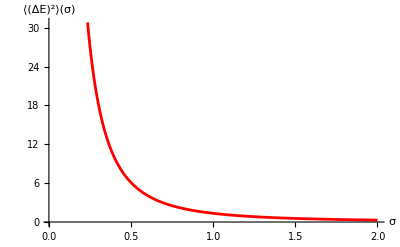

```mathematica
Plot[
LVEnergyVariance/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.01,2},
PlotStyle->Red,
AxesLabel->{"σ","⟨(ΔE)^2⟩(σ)"}
]
```

#### (#3.2.2.2): Plotting ⟨(ΔE)^2⟩(T) — remember that σ=1/(k_B T)—with test parameters:

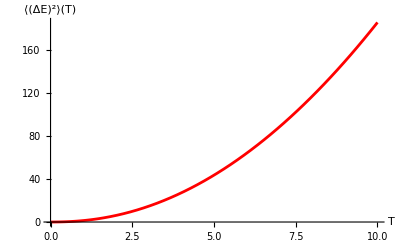

```mathematica
Plot[
LVEnergyVariance/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0,10},
PlotStyle->Red,
AxesLabel->{"T","⟨(ΔE)^2⟩(T)"}
]
```

#### (#3.2.2.3): Using Manipulate[] to see how things change with α and γ:

```mathematica
Manipulate[
Plot[
-T (α+γ-(α^2 PolyGamma[1,α/T])/T-(γ^2 PolyGamma[1,γ/T])/T),
{T,0.0001,10},
PlotStyle->Red,
AxesLabel->{"T","⟨(ΔE)^2⟩(T)"}
],{α,0.01,10.0},{γ,0.01,10.0}]
```

#### (#3.2.2.4): Zero-Temperature Limit:

```mathematica
Limit[LVEnergyVariance/.σ->1/T,T->0,Direction->-1]
```

ConditionalExpression[0, α>0&&γ>0]

It is probably the Trigamma Function thing sending things to 0 here.

```mathematica
Limit[ PolyGamma[1,α/T],T->0,Direction->-1]
```

ConditionalExpression[0, α>0]

## (#3.4): “Heat” Capacity, C_v=⟨(ΔE)^2⟩/(k_B T^2):

### (#3.4.1): Quantitative calculation using the standard formula:

```mathematica
LVHeatCapacity=σ^2 LVEnergyVariance//FullSimplify
```

σ (-α-γ+α^2 σ PolyGamma[1,α σ]+γ^2 σ PolyGamma[1,γ σ])

```mathematica
LVHeatCapacity/.σ->1/T
```

(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T

#### (#3.4.1): High-temperature limit:

First try a limit:

```mathematica
Limit[LVHeatCapacity/.σ->1/T,T->∞]
```

2

#### (#3.4.2): Low-temperature limit:

First try a limit:

```mathematica
Limit[LVHeatCapacity/.σ->1/T,T->0]
```

lim_(T→0) (-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T

Series expansion around T = 0 to first order:

```mathematica
Series[LVHeatCapacity/.σ->1/T,{T,0,1},Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

O[T]^0+Floor[Abs[Arg[α/T]]/π] ((π^2 α^2)/T^2+O[T]^1)+Cot[(π α)/T+O[T]^2]^2 Floor[Abs[Arg[α/T]]/π] ((π^2 α^2)/T^2+O[T]^1)+Floor[Abs[Arg[γ/T]]/π] ((π^2 γ^2)/T^2+O[T]^1)+Cot[(π γ)/T+O[T]^2]^2 Floor[Abs[Arg[γ/T]]/π] ((π^2 γ^2)/T^2+O[T]^1)

Series expansion around T = 0 to second order:

```mathematica
Series[LVHeatCapacity/.σ->1/T,{T,0,2},Assumptions->T∈PositiveReals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

(1+O[T]^1)+Floor[Abs[Arg[α/T]]/π] ((π^2 α^2)/T^2+O[T]^2)+Cot[(π α)/T+O[T]^2]^2 Floor[Abs[Arg[α/T]]/π] ((π^2 α^2)/T^2+O[T]^2)+Floor[Abs[Arg[γ/T]]/π] ((π^2 γ^2)/T^2+O[T]^2)+Cot[(π γ)/T+O[T]^2]^2 Floor[Abs[Arg[γ/T]]/π] ((π^2 γ^2)/T^2+O[T]^2)

### (#3.4.2): Plotting C_v(σ) with some test parameters:

#### (#3.4.2.1): Plotting C_v(σ) with test parameters:

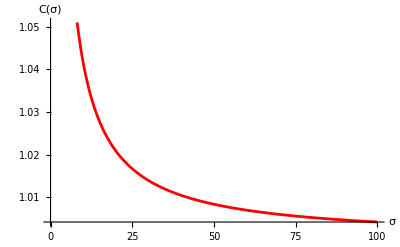

```mathematica
Plot[
LVHeatCapacity/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.001,100},
PlotStyle->Red,
AxesLabel->{"σ","C(σ)"}
]
```

#### (#3.4.2.2): Plotting C_v(T) — remember that σ = 1/(k_B T)—with test parameters:

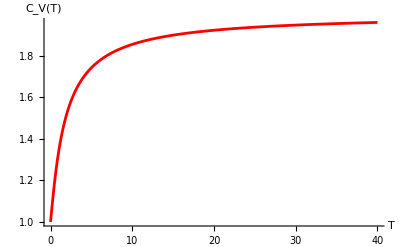

```mathematica
Plot[
LVHeatCapacity/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.0001,40},
PlotStyle->Red,
AxesLabel->{"T","C_V(T)"},
PlotRange->{{-3,20},{2.5,-0.1}}
]
```

Wow. It appears to asymptote to 2. I did not expect that. Let’s use a Manipulate[] function to verify that the boundary points of the curve do not change when we vary the parameters.

```mathematica
Manipulate[
Plot[
(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T,
{T,0.0001,40},
PlotStyle->Red,
AxesLabel->{"T","C_V(T)"},
PlotRange->{{-3,20},{2.5,-0.1}}
],{α,0.01,10.0},{γ,0.01,10.0}]
```

#### (#3.4.2.3): Trying to compute ΔS = (∫_T1)^T2 dT(C_v(T))/T :

```mathematica
(LVHeatCapacity/.σ->1/T)/T//FullSimplify
```

(-T (α+γ)+α^2 PolyGamma[1,α/T]+γ^2 PolyGamma[1,γ/T])/T^3

```mathematica
ChangeInLVEntropy=Integrate[
(-T (α+γ)+α^2 PolyGamma[1,α/T]+γ^2 PolyGamma[1,γ/T])/T^3,{T,T1,T2},
Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&γ∈PositiveReals&&T2>T1
]
```

Integrate[(-T (α+γ)+α^2 PolyGamma[1,α/T]+γ^2 PolyGamma[1,γ/T])/T^3,{T,T1,T2},Assumptions→T1∈ℝ&&T1>0&&T2∈ℝ&&T2>0&&α∈ℝ&&α>0&&γ∈ℝ&&γ>0&&T2>T1]

Can it do the integral of the PolyGamma only?

```mathematica
Integrate[ PolyGamma[1,α/T],{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

Integrate[PolyGamma[1,α/T],{T,T1,T2},Assumptions→T1∈ℝ&&T1>0&&T2∈ℝ&&T2>0&&α∈ℝ&&α>0&&T2>T1]

No it can’t. How about if we do PolyGamma over T?

```mathematica
Integrate[PolyGamma[1,α/T]/T,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

Integrate[PolyGamma[1,α/T]/T,{T,T1,T2},Assumptions→T1∈ℝ&&T1>0&&T2∈ℝ&&T2>0&&α∈ℝ&&α>0&&T2>T1]

Can’t do that either. Now, I think for PolyGamma over T^2 it can actually solve it:

```mathematica
Integrate[PolyGamma[1,α/T]/T^2,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

(PolyGamma[0,α/T1]-PolyGamma[0,α/T2])/α

It can do PolyGamma over T^2. But notice it cannot do PolyGamma over T^3:

```mathematica
Integrate[PolyGamma[1,α/T]/T^3,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

Integrate[PolyGamma[1,α/T]/T^3,{T,T1,T2},Assumptions→T1∈ℝ&&T1>0&&T2∈ℝ&&T2>0&&α∈ℝ&&α>0&&T2>T1]

And, just for fun, let’s try PolyGamma over T^4:

```mathematica
Integrate[PolyGamma[1,α/T]/T^4,{T,T1,T2},Assumptions->T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&T2>T1]
```

Integrate[PolyGamma[1,α/T]/T^4,{T,T1,T2},Assumptions→T1∈ℝ&&T1>0&&T2∈ℝ&&T2>0&&α∈ℝ&&α>0&&T2>T1]

```mathematica
ChangeInLVEntropy=NIntegrate[1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T/.α->2/3/.γ->1,{T,0.001,100.0}]
ChangeInLVEntropy=NIntegrate[1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T/.α->2/4/.γ->1,{T,0.001,100.0}]
ChangeInLVEntropy=NIntegrate[1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T/.α->2/5/.γ->1,{T,0.001,100.0}]
```

15.4991

15.6412

15.7517

## (#3.5): Entropy, S=-k_B θ^2∂/(∂θ)(ln(Z))/θ:

### (#3.5.1): Quantitative calculation using the standard formula:

```mathematica
LVEntropy=-σ^2 D[ Log[LVZIntegral]/σ,σ]//FullSimplify
```

σ (α+γ+α Log[β σ]+γ Log[δ σ])+Log[(β σ)^(-α σ) (δ σ)^(-γ σ) Gamma[α σ] Gamma[γ σ]]-σ (α PolyGamma[0,α σ]+γ PolyGamma[0,γ σ])

Checking against algebraic rewriting:

```mathematica
(σ(α+γ+γ Log[δ σ]-α PolyGamma[0,α σ]-γ PolyGamma[0,γ σ])+Log[(δ σ)^(-γ σ) Gamma[α σ] Gamma[γ σ]])-LVEntropy//FullSimplify
```

-α σ Log[β σ]+Log[(δ σ)^(-γ σ) Gamma[α σ] Gamma[γ σ]]-Log[(β σ)^(-α σ) (δ σ)^(-γ σ) Gamma[α σ] Gamma[γ σ]]

Check against another formula: S = ⟨E⟩/T+ k_B ln(Z) or S=k_B(β ⟨E⟩ + ln(Z))

```mathematica
LVEntropy-(σ LVEnergyAverage+ Log[LVZIntegral])//FullSimplify
```

0

In terms of temperature:

```mathematica
LVEntropy/.σ->1/T//FullSimplify
```

(α+γ+α Log[β/T]+γ Log[δ/T]+T Log[(β/T)^(-α/T) (δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-α PolyGamma[0,α/T]-γ PolyGamma[0,γ/T])/T

Yeah. It doesn’t do much... Let me see something else (just another algebraic rewriting):

```mathematica
FullSimplify[
(1/T(α(1-PolyGamma[0,α/T]+Log[β/T])+γ(1-PolyGamma[0,γ/T]+Log[δ/T]))+ Log[(β/T)^(-α/T)(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]])-(LVEntropy/.σ->1/T),
Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals
]
```

0

#### (#3.5.1.1): High-temperature limit:

First try a limit:

```mathematica
Limit[LVEntropy/.σ->1/T//FullSimplify,T->∞]
```

∞

Now try to expand:

```mathematica
Series[LVEntropy/.σ->1/T,{T,Infinity,1},Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

(2+Log[T^2/(α γ)])+(α+γ)/T+O[1/T]^2

#### (#3.5.1.2): Low-temperature limit:

Try a limit first:

```mathematica
Limit[LVEntropy/.σ->1/T//FullSimplify,T->0]
```

$Aborted

Now try to expand it to O(T):

```mathematica
Series[LVEntropy/.σ->1/T,{T,0,1},Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

Try to expand to O(T^2):

```mathematica
Series[LVEntropy/.σ->1/T,{T,0,2},Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

#### (#3.5.1.3): If the Entropy crosses 0 at some finite T, we should be able to figure out where that is:

```mathematica
Solve[(α+γ+γ Log[δ/T])/T+Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-(α PolyGamma[0,α/T]+γ PolyGamma[0,γ/T])/T==0,{T},Assumptions->T∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals]
```

```mathematica
Assuming[T∈Reals&&α∈Reals&&γ∈Reals&&δ∈Reals,
Reduce[(α+γ+γ Log[δ/T])/T+Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-(α PolyGamma[0,α/T]+γ PolyGamma[0,γ/T])/T==0,{T}]
]
```

```mathematica
FindRoot[(α+γ+γ Log[δ/T])/T+Log[(δ/T)^(-γ/T) Gamma[α/T] Gamma[γ/T]]-(α PolyGamma[0,α/T]+γ PolyGamma[0,γ/T])/T,{T,1}]
```

### (#3.5.2): Plotting S(θ) with some test parameters:

#### (#3.5.2.1): Plotting S(θ) with test parameters:

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,0.01,10},
PlotStyle->Red,
AxesLabel->{"σ [inverse temperature]","S(σ)"}
]
```

#### (#3.5.2.2): Plotting S(T) — remember that σ=1/(k_B T)—with test parameters:

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.01,2},
PlotStyle->Red,
AxesLabel->{"T [temperature]","S(T)"}
]
```

I need to see this: is there a bound for the entropy...

```mathematica
Plot[
LVEntropy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.006,0.1},
PlotStyle->Red,
AxesLabel->{"T [temperature]","S(T)"}
]
```

The major question is: Does the 0 point actually move, or is it for some random reason universal, the way the heat capacity behaved?

```mathematica
Plot[
LVEntropy/.α->1.1/.β->0.4/.γ->0.4/.δ->0.1/.σ->1/T,
{T,0.01,2},
PlotStyle->Red,
AxesLabel->{"T","S(T)"}
]
```

The 0 of the entropy has moved, indicating that there is in principle a nontrivial inverse problem to solve for this critical value of the temperature...

### (#3.5.2): Entropy of Mixing:

Entropy is an equilibrium (additive!) state function. So, let’s compare the entropy before and after mixing of two systems at the same temperature:

```mathematica
CombinedSystemsLVEntropy=σ (αC+γC+γC Log[δC σ])+Log[(δC σ)^(-γC σ) Gamma[αC σ] Gamma[γC σ]]-σ (αC PolyGamma[0,αC σ]+γC PolyGamma[0,γC σ]);
TwoSeparatedSystemsLVEntropy=(σ (α1+γ1+γ1 Log[δ1 σ])+Log[(δ1 σ)^(-γ1 σ) Gamma[α1 σ] Gamma[γ1 σ]]-σ (α1 PolyGamma[0,α1 σ]+γ1 PolyGamma[0,γ1 σ]))+(σ (α2+γ2+γ2 Log[δ2 σ])+Log[(δ2 σ)^(-γ2 σ) Gamma[α2 σ] Gamma[γ2 σ]]-σ (α2 PolyGamma[0,α2 σ]+γ2 PolyGamma[0,γ2 σ]));
```

```mathematica
FullSimplify[CombinedSystemsLVEntropy-TwoSeparatedSystemsLVEntropy,Assumptions->σ∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&γ∈PositiveReals&&δ∈PositiveReals]
```

-σ (α1+γ1+γ1 Log[δ1 σ])-σ (α2+γ2+γ2 Log[δ2 σ])+σ (αC+γC+γC Log[δC σ])-Log[(δ1 σ)^(-γ1 σ) Gamma[α1 σ] Gamma[γ1 σ]]-Log[(δ2 σ)^(-γ2 σ) Gamma[α2 σ] Gamma[γ2 σ]]+Log[(δC σ)^(-γC σ) Gamma[αC σ] Gamma[γC σ]]+σ (α1 PolyGamma[0,α1 σ]+γ1 PolyGamma[0,γ1 σ])+σ (α2 PolyGamma[0,α2 σ]+γ2 PolyGamma[0,γ2 σ])-σ (αC PolyGamma[0,αC σ]+γC PolyGamma[0,γC σ])

### (#3.5.3): Entropy as Temperature Changes?

Remember how we couldn’t do the integral for ΔS = ∫dT (C(T))/T? Let’s try to do it now:

```mathematica
FullSimplify[(LVEntropy/.σ->1/T2)-(LVEntropy/.σ->1/T1),T1∈PositiveReals&&T2∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&γ∈PositiveReals&&δ∈PositiveReals]
```

((T1-T2) (α+γ)+T1 T2 Log[(Gamma[α/T2] Gamma[γ/T2])/(Gamma[α/T1] Gamma[γ/T1])]+T2 α PolyGamma[0,α/T1]+T2 γ PolyGamma[0,γ/T1]-T1 (α PolyGamma[0,α/T2]+γ PolyGamma[0,γ/T2]))/(T1 T2)

First of all, it is astounding that the dependence on β and δ just goes away in this derivative... Obviously, it’s just math, but it is nonetheless wildly unexpected.

```mathematica
D[LVEntropy/.σ->1/T,T]//FullSimplify
```

(-T (α+γ)+α^2 PolyGamma[1,α/T]+γ^2 PolyGamma[1,γ/T])/T^3

```mathematica
FullSimplify[D[LVEntropy/.σ->1/T,T],T∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&γ∈PositiveReals&&δ∈PositiveReals]
```

(-T (α+γ)+α^2 PolyGamma[1,α/T]+γ^2 PolyGamma[1,γ/T])/T^3

Rewriting using some algebra:

```mathematica
(FullSimplify[D[LVEntropy/.σ->1/T,T],T∈PositiveReals&&α∈PositiveReals&&β∈PositiveReals&&γ∈PositiveReals&&δ∈PositiveReals])-(1/T(-α-γ+(α^2 PolyGamma[1,α/T])/T+(γ^2 PolyGamma[1,γ/T])/T)/T)//FullSimplify
```

0

Yup. It’s the same.

## (#3.6): Free Energy, F=-k_BT log(Z):

### (#3.6.1): Quantitative calculation using the standard formula:

```mathematica
LVFreeEnergy=-1/σ Log[LVZIntegral]//FullSimplify
```

-Log[(β σ)^(-α σ) (δ σ)^(-γ σ) Gamma[α σ] Gamma[γ σ]]/σ

### (#3.6.2): Plotting F(θ) with some test parameters:

#### (#3.6.2.1): Plotting F(θ) with test parameters:

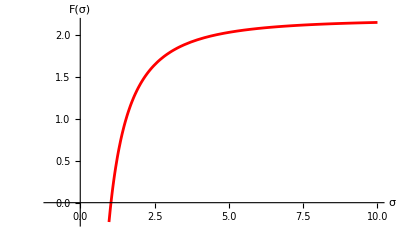

```mathematica
Plot[
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1,
{σ,-1.0,10.0},
PlotStyle->Red,
AxesLabel->{"σ","F(σ)"}
]
```

#### (#3.6.2.2): Where is it crossing 0?

```mathematica
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1
```

-Log[2^(-4 σ/3) 3^(2 σ/3) σ^(-5 σ/3) Gamma[(2 σ)/3] Gamma[σ]]/σ

```mathematica
NSolve[-Log[2^(-4 σ/3) 3^(2 σ/3) σ^(-5 σ/3) Gamma[(2 σ)/3] Gamma[σ]]/σ==0,σ]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-Log[2^(-4 σ/3) 3^(2 σ/3) σ^(-5 σ/3) Gamma[(2 σ)/3] Gamma[σ]]/σ==0,σ]

#### (#3.6.2.3): Plotting F(T) — remember that θ = 1/(k_B T)—with test parameters:

General::munfl: 1/99.7982^166.33 is too small to represent as a normalized machine number; precision may be lost.

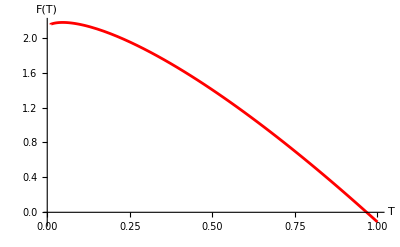

```mathematica
Plot[
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T,
{T,0.01,1},
PlotStyle->Red,
AxesLabel->{"T","F(T)"}
]
```

#### (#3.6.2.4): Where is it crossing 0?

```mathematica
LVFreeEnergy/.α->2/3/.β->4/3/.γ->1/.δ->1/.σ->1/T
```

-T Log[2^(-4/3/T) 3^(2/3/T) (1/T)^(-5/3/T) Gamma[2/(3 T)] Gamma[1/T]]

```mathematica
NSolve[-T Log[2^(-4/3/T) 3^(2/3/T) (1/T)^(-5/3/T) Gamma[2/(3 T)] Gamma[1/T]]==0,T]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[-T Log[2^(-4/3/T) 3^(2/3/T) (1/T)^(-5/3/T) Gamma[2/(3 T)] Gamma[1/T]]==0,T]

### (#3.6.3): Verifying that indeed C_V=-T (∂^2)_T F holds here:

Yup, it works:

```mathematica
FullSimplify[-T(D[LVFreeEnergy/.σ->1/T,{T,2}])-LVHeatCapacity/.σ->1/T]
```

0

### (#3.6.4): Derivatives of F(T) with respect to “microscopic parameters”

#### (#3.6.4.1): ((∂F(T))/(∂α))_(T,β,γ,δ):

```mathematica
D[LVFreeEnergy/.σ->1/T,α]//FullSimplify
```

Log[β/T]-PolyGamma[0,α/T]

Check for discontinuities:

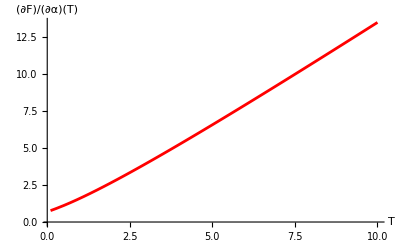

```mathematica
Plot[
D[LVFreeEnergy/.σ->1/T,α]/.α->2/3/.β->4/3/.γ->1/.δ->1,
{T,0.1,10},
PlotStyle->Red,
AxesLabel->{"T","(∂F)/(∂α)(T)"}
]
```

#### (#3.6.4.2): ((∂F(T))/(∂β))_(T,α,γ,δ):

```mathematica
D[LVFreeEnergy/.σ->1/T,β]//FullSimplify
```

α/β

This is obviously flat:

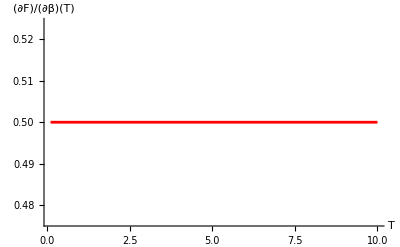

```mathematica
Plot[
D[LVFreeEnergy/.σ->1/T,β]/.α->2/3/.β->4/3/.γ->1/.δ->1,
{T,0.1,10},
PlotStyle->Red,
AxesLabel->{"T","(∂F)/(∂β)(T)"}
]
```

#### (#3.6.4.3): ((∂F(T))/(∂γ))_(T,α,β,δ):

Should be extremely similar to (#3.6.4.1):

```mathematica
D[LVFreeEnergy/.σ->1/T,γ]//FullSimplify
```

Log[δ/T]-PolyGamma[0,γ/T]

#### (#3.6.4.4): ((∂F(T))/(∂δ))_(T,α,β,γ):

Should be γ/δ:

```mathematica
D[LVFreeEnergy/.σ->1/T,δ]//FullSimplify
```

γ/δ

## (#3.X): Information Geometry:

#### (#3.X.Y): Fischer Information Metric:

The metric is one-dimensional because there is only one Lagrange multiplier in the Partition Function above.

```mathematica
FischerMetric11LV=D[-Log[LVZIntegral],{θ, 2}]//FullSimplify
```

## (#4): Corresponding “Maxwell-Boltzmann Velocity Distribution”

## (#4.1): “Making” it a Probability Distribution:

```mathematica
Integrate[cp LVZp[σ],{p,-∞,∞},Assumptions->cp ∈Reals]
```

Now fix the constant:

```mathematica
MaxBoltMomentumDistribution=1/((δ σ)^(-γ σ) Gamma[γ σ])LVZp[σ];
```

### (#4.1.1): Mean Momentum:

```mathematica
Integrate[p^1 MaxBoltMomentumDistribution,{p,-∞,∞}]
```

### (#4.1.2): Most Probable Momentum:

```mathematica
Solve[D[MaxBoltMomentumDistribution,p]==0,p]
```

### (#4.1.3): Other Moments:

```mathematica
Integrate[p^n MaxBoltMomentumDistribution,{p,-∞,∞},Assumptions->n∈PositiveIntegers]
```

## (#X): Keeping the Rotation Angle ϕ Open:

## (#X.1): Transforming to the Hamiltonian:

### (#X.1.1): Original Dynamical Invariant:

```mathematica
LVDynInvariant=δ x - γ Log[x]+β y-α Log[y];
```

### (#X.1.2): Verifying original coordinate transformation works:

```mathematica
FullSimplify[
LVHamiltonian[q,p]-LVDynInvariant/.y->Exp[q]/.x->Exp[p],
Assumptions->x∈Reals&&y∈Reals&&q∈Reals&&p∈Reals]
```

### (#X.1.3): Now, do the original transformation for (x, y) and (q, p) was for ϕ=π/4:

Must understand that we flipped the “chirality” when we assigned q to log(y) and p to log(x), and that’s why we have flipped the order of the logs in this column vector below:

```mathematica
RotationMatrix[π/4].{Log[y],Log[x]}//MatrixForm
```

### (#X.1.4): Here is then the arbitrary transformation between (x, y) and (q, p) for any ϕ:

```mathematica
RotationMatrix[ϕ].{Log[y],Log[x]}//MatrixForm
```

```mathematica
Solve[
{p==Cos[ϕ] Log[x]+Log[y] Sin[ϕ],q==Cos[ϕ] Log[y]-Log[x] Sin[ϕ]},
{x,y}]
```

```mathematica
FullSimplify[
LVDynInvariant/.y->ⅇ^(-(-p Csc[ϕ]-q Cot[ϕ] Csc[ϕ])/(1+Cot[ϕ]^2))/.x->ⅇ^(-(-p Cos[ϕ]+q Sin[ϕ])/(Cos[ϕ]^2+Sin[ϕ]^2)),
Assumptions->q∈Reals&&p∈Reals&&ϕ∈Reals
]
```

## (#X.2): Constructing the Canonical Ensemble Partition Function:

### (#X.2.1): Arbitrary Angle Hamiltonian:

```mathematica
LVRotatedHamiltonian[q_,p_,ϕ_]:=ⅇ^(q Cos[ϕ]+p Sin[ϕ]) β+ⅇ^(p Cos[ϕ]-q Sin[ϕ]) δ-(q α+p γ) Cos[ϕ]+(-p α+q γ) Sin[ϕ];
```

Quickly checking that this generalizes the previous Hamiltonian at ϕ = 0;

```mathematica
FullSimplify[
LVRotatedHamiltonian[q,p,0]-LVHamiltonian[q,p],
α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals
]
```

### (#X.2.2): Arbitrary Angle Canonical Ensemble Partition Function:

```mathematica
LVRotatedZ[σ_]:=Exp[-σ LVRotatedHamiltonian[q,p,ϕ]];
```

### (#X.2.3): Attempting Integration of the Arbitrary ϕ Partition Function:

```mathematica
LVRotatedZIntegral=Integrate[
LVRotatedZ[σ],{q,-∞,∞},{p,-∞,∞},
Assumptions->σ∈Reals&&α∈Reals&&β ∈Reals&&γ∈Reals&&δ∈Reals&&ϕ∈Reals
]
```